```mathematica
(* Number conserving flat band Josephson junction model for Subscript[E, C]=0. Solved by Fourier transforming into a basis of ϕ states and exactly diagonalised. Minimal example of the setup to start plotting. *)
```

## INIT

## DEFINITIONS

```mathematica
<<sneg`;
```

sneg 2.0.3 Copyright (C) 2002-2022 Rok Zitko

```mathematica
snegfermionoperators[d, f];
snegrealconstants[mL, mR, U, α, ϵimp, v, vL, vR, Γ,ϕ,tp,ϕext];
```

```mathematica
(* NAMING SPIN *)
{nDO=-1,nUP=+1,n2=2,n0=0}
nσ[σ_]:=If[σ==UP,nUP,nDO];
```

{-1,1,2,0}

```mathematica
(* DEFINITIONS FOR Ket[] *)
(* Bra and Ket conjugation *)
conj[Ket[k___]]:=Bra[k];
conj[Bra[b___]]:=Ket[b];
(* Orthogonality *)
nc[a___,Bra[b___],Ket[k___],e___]/;pairpattern[{b},{k}]:=KroneckerDelta[{b},{k}] nc[a,e];
nc[a___,Bra[b___],d[___],Ket[k___],e___]/;pairpattern[{b},{k}]:=KroneckerDelta[{b},{k}] nc[a,e];
(* KroneckerDelta is a number*)
nc[a___, KroneckerDelta[x_, y_], b___] := KroneckerDelta[x, y]nc[a, b];
(* Annihilates zero state on QD *)
nc[a___,d[AN,σ_],Ket[__]]:=0;
(*THIS EXPECTED VALUE IS ZERO*)
nc[Bra[__],d[CR,σ1_],d[CR,σ2_],Ket[__]]:=0
```

```mathematica
(* COMPUTE THE DIAGONAL ELEMENT - THE ENERGY OF A STATE. *)
(* This is in the approximation without finite size effects. SIAM at the impurity, and α for each quasiparticle in the SC. *)
stateEnergy[state_]:= Module[{},
nc[a___, EE,imp___,ket:Ket[ϕ_,nL_,nR_]]:=nc[a,(U hubbard[d[]]+ϵimp number[d[]]),imp,ket ]+α(Abs[nL]+Abs[nR])nc[a, imp, ket];
nc[conj[state],EE,state]
];
(* Prints the most prominent elements of an eigenvector. *)
bvec[i_Integer]:=Transpose[{vec[[i]], bb}]//MatrixForm
(*bvec[vec_List]:=Transpose[{vec, bb}]//MatrixForm*)
bvec[vec_List]:=Transpose[{Abs[vec],Arg[vec]/π, bb}]//MatrixForm
multbvec[vec_]:=Table[{Abs[nc[conj[i],vec]],Arg[nc[conj[i],vec]]/π, i},{i, bb}]//MatrixForm
```

```mathematica
phSymmetric={ϵimp->-U/2,vL->v, vR->v}
LRsymmetric = {vL->v,vR->v}
```

{ϵimp→-U/2,vL→v,vR→v}

{vL→v,vR→v}

```mathematica
(* Total number of quasiparticles *)
nc[a___, nQP,qd___,ket:Ket[ϕ_,nL_,nR_]]:=(Abs[nL]+Abs[nR])nc[a, qd,ket];
(* Total number of unpaired particles *)
nc[a___, nUP,qd___,ket:Ket[ϕ_,nL_,nR_]]:=nc[a,number[d[]],qd,ket]+(Abs[nL]+Abs[nR])nc[a, qd,ket];
nQP[state_]:=Module[{},
nc[conj[state],nQP,state]
]
```

```mathematica
Transpose[{ColorData[97,"ColorList"],Defer[RGBColor]@@@ColorData[97,"ColorList"]}]//MatrixForm
```

(RGBColor[0.368417, 0.506779, 0.709798] | RGBColor[0.368417,0.506779,0.709798]
RGBColor[0.880722, 0.611041, 0.142051] | RGBColor[0.880722,0.611041,0.142051]
RGBColor[0.560181, 0.691569, 0.194885] | RGBColor[0.560181,0.691569,0.194885]
RGBColor[0.922526, 0.385626, 0.209179] | RGBColor[0.922526,0.385626,0.209179]
RGBColor[0.528488, 0.470624, 0.701351] | RGBColor[0.528488,0.470624,0.701351]
RGBColor[0.772079, 0.431554, 0.102387] | RGBColor[0.772079,0.431554,0.102387]
RGBColor[0.363898, 0.618501, 0.782349] | RGBColor[0.363898,0.618501,0.782349]
RGBColor[1, 0.75, 0] | RGBColor[1,0.75,0]
RGBColor[0.647624, 0.37816, 0.614037] | RGBColor[0.647624,0.37816,0.614037]
RGBColor[0.571589, 0.586483, 0.] | RGBColor[0.571589,0.586483,0.]
RGBColor[0.915, 0.3325, 0.2125] | RGBColor[0.915,0.3325,0.2125]
RGBColor[0.40082222609352647, 0.5220066643438841, 0.85] | RGBColor[0.400822,0.522007,0.85]
RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142] | RGBColor[0.972829,0.621644,0.073362]
RGBColor[0.736782672705901, 0.358, 0.5030266573755369] | RGBColor[0.736783,0.358,0.503027]
RGBColor[0.28026441037696703, 0.715, 0.4292089322474965] | RGBColor[0.280264,0.715,0.429209])

```mathematica
(* Some nice colors *)
blue=RGBColor[0.368417,0.506779,0.709798]
red=RGBColor[0.922526,0.385626,0.209179]
green=RGBColor[0.560181,0.691569,0.194885]
orange=RGBColor[0.880722,0.611041,0.142051]
```

RGBColor[0.368417, 0.506779, 0.709798]

RGBColor[0.922526, 0.385626, 0.209179]

RGBColor[0.560181, 0.691569, 0.194885]

RGBColor[0.880722, 0.611041, 0.142051]

```mathematica
$PlotTheme={"Scientific"}
```

{Scientific}

## DOUBLET BASIS

```mathematica
(* 1 QP states *)
ψ100[ϕ_] := nc[d[CR, UP], Ket[ϕ,n0,n0]]
ψ010[ϕ_] := nc[Ket[ϕ,nUP,n0]]
ψ001[ϕ_] := nc[Ket[ϕ,n0,nUP]]

(* 3 QP states *)
ψ210[ϕ_]:=nc[d[CR, UP],d[CR, DO], Ket[ϕ,nUP,n0]]
ψ201[ϕ_]:=nc[d[CR, UP],d[CR, DO], Ket[ϕ,n0,nUP]]
ψ120[ϕ_]:=nc[d[CR,UP], Ket[ϕ,n2,n0]]
ψ021[ϕ_]:=nc[Ket[ϕ,n2,nUP]]
ψ012[ϕ_]:=nc[Ket[ϕ,nUP,n2]]
ψ102[ϕ_]:=nc[d[CR, UP],Ket[ϕ,n0,n2]]
(**)
ψS12[ϕ_]:=(nc[d[CR, DO], Ket[ϕ,nUP,nUP]]-nc[d[CR, UP], Ket[ϕ,nDO,nUP]])/Sqrt[2]
ψ3qp[ϕ_]:=( nc[d[CR, DO], Ket[ϕ,nUP,nUP]] + nc[d[CR,UP], Ket[ϕ,nDO,nUP]]- 2nc[d[CR,UP], Ket[ϕ,nUP,nDO]] )/Sqrt[6]

(* 5 QP states *)
ψ221[ϕ_]:=nc[d[CR, UP], d[CR, DO], Ket[ϕ,n2,nUP]]
ψ212[ϕ_]:=nc[d[CR, UP], d[CR, DO], Ket[ϕ,nUP,n2]]
ψ122[ϕ_]:=nc[d[CR, UP], Ket[ϕ,n2,n2]]

(* This list defines the order of the basis states! *)
doubletBasis[ϕ_] := {ψ100[ϕ] , ψ010[ϕ], ψ001[ϕ],ψ210[ϕ],ψ201[ϕ],ψ120[ϕ],ψ021[ϕ],ψ012[ϕ],ψ102[ϕ],ψS12[ϕ],ψ3qp[ϕ],ψ221[ϕ],ψ212[ϕ],ψ122[ϕ]}
```

```mathematica
doubletBlockInsideΔm=({{0, vL/(√2), vR/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {vL/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {vR/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -vL/(√2), 0, 0, 0, vR/2, (√3 vR)/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -vR/(√2), -vL, 0, 0, 0, 0}, {0, 0, 0, -vL/(√2), 0, 0, vR/(√2), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, vR/(√2), 0, 0, 0, -vL, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, vL/(√2), vR/2, (√3 vR)/2, 0, 0, 0}, {0, 0, 0, 0, -vR/(√2), 0, 0, vL/(√2), 0, 0, 0, 0, 0, 0}, {0, 0, 0, vR/2, -vL, 0, -vL, vR/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, (√3 vR)/2, 0, 0, 0, (√3 vR)/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -vR/(√2)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -vL/(√2)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -vR/(√2), -vL/(√2), 0}});
doubletBlockOutsideΔm=({{0, 0, 0, -(vL Exp[-ⅈ ϕ])/(√2), -vR/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -(vL Exp[-ⅈ ϕ])/(√2), 0, 0, 0, 1/2 vR, 1/2 √3 vR, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -vR/(√2), -vL Exp[-ⅈ ϕ], 0, 0, 0, 0}, {-(vL Exp[ⅈ ϕ])/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-vR/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -(vL Exp[ⅈ ϕ])/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, -(vR Exp[ⅈ ϕ])/(√2), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(vR Exp[ⅈ ϕ])/(√2)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -vL/(√2)}, {0, 0, -vR/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, -vL/(√2), 0}, {0, 1/2 vR, -vL Exp[ⅈ ϕ], 0, 0, 0, 0, 0, 0, 0, 0, vL, -1/2 vR Exp[ⅈ ϕ], 0}, {0, 1/2 √3 vR, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/2 √3 vR Exp[ⅈ ϕ], 0}, {0, 0, 0, 0, 0, -(vR Exp[-ⅈ ϕ])/(√2), 0, 0, 0, vL, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -vL/(√2), -1/2 vR Exp[-ⅈ ϕ], -1/2 √3 vR Exp[-ⅈ ϕ], 0, 0, 0}, {0, 0, 0, 0, 0, 0, -(vR Exp[-ⅈ ϕ])/(√2), -vL/(√2), 0, 0, 0, 0, 0, 0}});
doubletBlock=doubletBlockInsideΔm+doubletBlockOutsideΔm;
HermitianMatrixQ[%]
```

True

(U/2+ϵimp | vL/(√2) | vR/(√2) | -(ⅇ^(-ⅈ ϕ) vL)/(√2) | -vR/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
vL/(√2) | U/2+α | 0 | 0 | 0 | -(ⅇ^(-ⅈ ϕ) vL)/(√2) | 0 | 0 | 0 | vR/2 | (√3 vR)/2 | 0 | 0 | 0
vR/(√2) | 0 | U/2+α | 0 | 0 | 0 | 0 | 0 | -vR/(√2) | -ⅇ^(-ⅈ ϕ) vL | 0 | 0 | 0 | 0
-(ⅇ^(ⅈ ϕ) vL)/(√2) | 0 | 0 | (3 U)/2+α+2 ϵimp | 0 | -vL/(√2) | 0 | 0 | 0 | vR/2 | (√3 vR)/2 | 0 | 0 | 0
-vR/(√2) | 0 | 0 | 0 | (3 U)/2+α+2 ϵimp | 0 | 0 | 0 | -vR/(√2) | -vL | 0 | 0 | 0 | 0
0 | -(ⅇ^(ⅈ ϕ) vL)/(√2) | 0 | -vL/(√2) | 0 | U/2+2 α+ϵimp | vR/(√2) | 0 | 0 | 0 | 0 | -(ⅇ^(ⅈ ϕ) vR)/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | vR/(√2) | 1/2 (U+6 α) | 0 | 0 | -vL | 0 | 0 | 0 | -(ⅇ^(ⅈ ϕ) vR)/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (U+6 α) | vL/(√2) | vR/2 | (√3 vR)/2 | 0 | 0 | -vL/(√2)
0 | 0 | -vR/(√2) | 0 | -vR/(√2) | 0 | 0 | vL/(√2) | U/2+2 α+ϵimp | 0 | 0 | 0 | -vL/(√2) | 0
0 | vR/2 | -ⅇ^(ⅈ ϕ) vL | vR/2 | -vL | 0 | -vL | vR/2 | 0 | U/2+2 α+ϵimp | 0 | vL | -1/2 ⅇ^(ⅈ ϕ) vR | 0
0 | (√3 vR)/2 | 0 | (√3 vR)/2 | 0 | 0 | 0 | (√3 vR)/2 | 0 | 0 | U/2+2 α+ϵimp | 0 | -1/2 √3 ⅇ^(ⅈ ϕ) vR | 0
0 | 0 | 0 | 0 | 0 | -(ⅇ^(-ⅈ ϕ) vR)/(√2) | 0 | 0 | 0 | vL | 0 | (3 U)/2+3 α+2 ϵimp | 0 | -vR/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -vL/(√2) | -1/2 ⅇ^(-ⅈ ϕ) vR | -1/2 √3 ⅇ^(-ⅈ ϕ) vR | 0 | (3 U)/2+3 α+2 ϵimp | -vL/(√2)
0 | 0 | 0 | 0 | 0 | 0 | -(ⅇ^(-ⅈ ϕ) vR)/(√2) | -vL/(√2) | 0 | 0 | 0 | -vR/(√2) | -vL/(√2) | U/2+4 α+ϵimp)

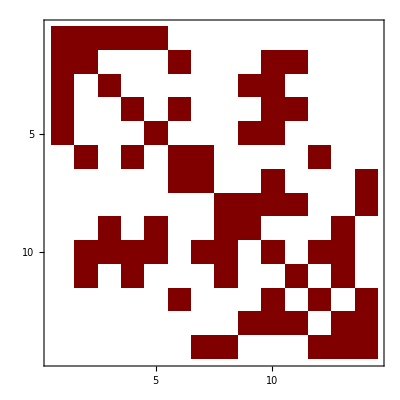

```mathematica
doubletDiagonalElements = DiagonalMatrix[FullSimplify[U/2 + stateEnergy[#]]&[doubletBasis[ϕ]]];
doubletBlock = doubletBlock + doubletDiagonalElements;
%//MatrixForm
MatrixPlot[%]
```

## SINGLET BASIS

```mathematica
(* SINGLET BASIS STATES: *)
(* 0 QP *)
ϕ0[ϕ_]:= nc[Ket[ϕ,n0,n0]];
(* 2 QP *)
ϕ002[ϕ_]:= nc[Ket[ϕ,n0,n2]];
ϕ020[ϕ_]:= nc[Ket[ϕ,n2,n0]];
ϕ200[ϕ_]:= nc[d[CR, UP], d[CR, DO],Ket[ϕ,n0,n0]];
ϕs12[ϕ_]:= (nc[d[CR, UP],Ket[ϕ,nDO,n0]]-nc[d[CR, DO],Ket[ϕ,nUP,n0]])/Sqrt[2];
ϕs13[ϕ_]:= (nc[d[CR, UP],Ket[ϕ,n0,nDO]]-nc[d[CR, DO],Ket[ϕ,n0,nUP]])/Sqrt[2];
ϕs23[ϕ_]:= (nc[Ket[ϕ,nDO,nUP]]-nc[Ket[ϕ,nUP,nDO]])/Sqrt[2];
(* 4 QP *)
ϕ022[ϕ_]:= nc[Ket[ϕ,n2,n2]];
ϕ202[ϕ_]:= nc[d[CR,UP],d[CR, DO],Ket[ϕ,n0,n2]];
ϕ220[ϕ_]:= nc[d[CR,UP],d[CR, DO],Ket[ϕ,n2,n0]];
ϕs412[ϕ_]:= (nc[d[CR,DO],Ket[ϕ,nUP,n2]]-nc[d[CR,UP],Ket[ϕ,nDO,n2]])/Sqrt[2];
ϕs413[ϕ_]:= (nc[d[CR,DO],Ket[ϕ,n2,nUP]]-nc[d[CR,UP],Ket[ϕ,n2,nDO]])/Sqrt[2];
ϕs423[ϕ_]:= (nc[d[CR,UP], d[CR, DO],Ket[ϕ,nUP,nDO]]-nc[d[CR,UP], d[CR, DO],Ket[ϕ,nDO,nUP]])/Sqrt[2];
(* 6 QP *)
ϕ6[ϕ_] := nc[d[CR, UP], d[CR, DO], Ket[ϕ,n2,n2]];

(* This list defines the order of the basis states! *)
singletBasis[ϕ_] := {ϕ0[ϕ] , ϕ002[ϕ], ϕ020[ϕ],ϕ200[ϕ],ϕs12[ϕ],ϕs13[ϕ],ϕs23[ϕ],ϕ022[ϕ],ϕ202[ϕ],ϕ220[ϕ],ϕs412[ϕ],ϕs413[ϕ],ϕs423[ϕ],ϕ6[ϕ]}
```

```mathematica
(* The hopping block consists of hopping terms in the same block, ie. Δm<->Δm and Δm+1<->Δm+1, and terms between the blocks, Δm<->Δm+1, Δm<->Δm-1 and Δm+1<->Δm+2. *)
(* The unit cell was chosen to contain (Δm, Δm+1) and all hoppin outside of it gets an Exp[ⅈϕ] factor. *)
(* The two blocks are split here. *)
(* Orange blocks are Δm, blue are Δm+1*)
singletBlockInsideΔm=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, vR, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, vL, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, vL, vR, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, vL, vL, 0, 0, -vR/(√2), 0, 0, 0, 0, 0, 0, 0}, {0, vR, 0, vR, 0, 0, -vL/(√2), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -vR/(√2), -vL/(√2), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -vL, -vR, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -vL, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -vR, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -vL, -vL, 0, 0, 0, vR/(√2), 0}, {0, 0, 0, 0, 0, 0, 0, -vR, 0, -vR, 0, 0, vL/(√2), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, vR/(√2), vL/(√2), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
singletBlockOutsideΔm=({{0, 0, 0, 0, vL Exp[-ⅈ ϕ], vR, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -vL, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -vR Exp[ⅈ ϕ], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {vL Exp[ⅈ ϕ], 0, 0, 0, 0, 0, 0, 0, 0, -vL, 0, 0, -(vR Exp[ⅈ ϕ])/(√2), 0}, {vR, 0, 0, 0, 0, 0, 0, 0, -vR Exp[ⅈ ϕ], 0, 0, 0, -vL/(√2), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(vR Exp[ⅈ ϕ])/(√2), -vL/(√2), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -vR Exp[-ⅈ ϕ], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -vL, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -vL, 0, 0, 0, 0, -(vR Exp[-ⅈ ϕ])/(√2), 0, 0, 0, 0, 0, 0, vL Exp[-ⅈ ϕ]}, {0, 0, -vR Exp[-ⅈ ϕ], 0, 0, 0, -vL/(√2), 0, 0, 0, 0, 0, 0, vR}, {0, 0, 0, 0, -(vR Exp[-ⅈ ϕ])/(√2), -vL/(√2), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, vL Exp[ⅈ ϕ], vR, 0, 0}});
singletBlock=singletBlockInsideΔm+singletBlockOutsideΔm;
HermitianMatrixQ[%]
```

True

```mathematica
singletDiagonalElements = DiagonalMatrix[FullSimplify[U/2 + stateEnergy[#]]&[singletBasis[ϕ]]];
```

```mathematica
singletBlock = singletBlock + singletDiagonalElements;
%//MatrixForm
MatrixPlot[%];
```

(U/2 | 0 | 0 | 0 | ⅇ^(-ⅈ ϕ) vL | vR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (U+4 α) | 0 | 0 | 0 | vR | 0 | 0 | 0 | 0 | -vL | 0 | 0 | 0
0 | 0 | 1/2 (U+4 α) | 0 | vL | 0 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ ϕ) vR | 0 | 0
0 | 0 | 0 | (3 U)/2+2 ϵimp | vL | vR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅇ^(ⅈ ϕ) vL | 0 | vL | vL | U/2+α+ϵimp | 0 | -vR/(√2) | 0 | 0 | -vL | 0 | 0 | -(ⅇ^(ⅈ ϕ) vR)/(√2) | 0
vR | vR | 0 | vR | 0 | U/2+α+ϵimp | -vL/(√2) | 0 | -ⅇ^(ⅈ ϕ) vR | 0 | 0 | 0 | -vL/(√2) | 0
0 | 0 | 0 | 0 | -vR/(√2) | -vL/(√2) | 1/2 (U+4 α) | 0 | 0 | 0 | -(ⅇ^(ⅈ ϕ) vR)/(√2) | -vL/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (U+8 α) | 0 | 0 | -vL | -vR | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ ϕ) vR | 0 | 0 | (3 U)/2+2 (α+ϵimp) | 0 | -vL | 0 | 0 | 0
0 | 0 | 0 | 0 | -vL | 0 | 0 | 0 | 0 | (3 U)/2+2 (α+ϵimp) | 0 | -vR | 0 | 0
0 | -vL | 0 | 0 | 0 | 0 | -(ⅇ^(-ⅈ ϕ) vR)/(√2) | -vL | -vL | 0 | U/2+3 α+ϵimp | 0 | vR/(√2) | ⅇ^(-ⅈ ϕ) vL
0 | 0 | -ⅇ^(-ⅈ ϕ) vR | 0 | 0 | 0 | -vL/(√2) | -vR | 0 | -vR | 0 | U/2+3 α+ϵimp | vL/(√2) | vR
0 | 0 | 0 | 0 | -(ⅇ^(-ⅈ ϕ) vR)/(√2) | -vL/(√2) | 0 | 0 | 0 | 0 | vR/(√2) | vL/(√2) | (3 U)/2+2 (α+ϵimp) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ ϕ) vL | vR | 0 | (3 U)/2+4 α+2 ϵimp)

## PLOTS

{α→1,U→0.,ϵimp→0.05,v→0.3}

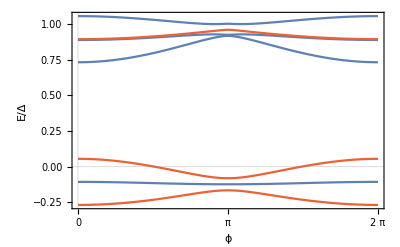

```mathematica
(* Spectrum vs ϕ at U=0, ϵimp=5 *)
params = {α->1,U->0.,ϵimp->0.05,v->0.3}
matD =(doubletBlock/.LRsymmetric//.params);
matS =(singletBlock/.LRsymmetric//.params);
Plot[{
Sort[Eigenvalues[matD]][[1;;4]],
Sort[Eigenvalues[matS]][[1;;3]]
},{ϕ,0.,2.π}, PlotStyle->{blue,red},FrameLabel->{"ϕ","E/Δ"}, AxesOrigin->{0,0}, PlotRange->All,FrameStyle->Black,FrameTicks->{{Automatic,None},{{0,π,2π},None}},LabelStyle->FontSize->20]
```